## Basic

(D | 1 | 0 | 0 | 0
1 | D | 1 | 0 | 0
0 | 1 | D | 1 | 0
0 | 0 | 1 | D | 1
0 | 0 | 0 | 1 | D)

(a0 | a1 | a2 | a3 | a4
-a | 0 | a | 0 | 0
0 | -a | 0 | a | 0
0 | 0 | -a | 0 | a
-a4 | -a3 | -a2 | -a1 | -a0)

{0,-1.61861+2.23062 ⅈ,1.61861-2.23062 ⅈ,-1.61861-2.23062 ⅈ,1.61861+2.23062 ⅈ}

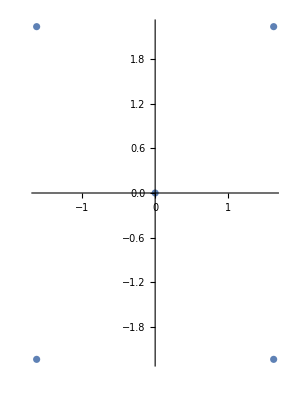

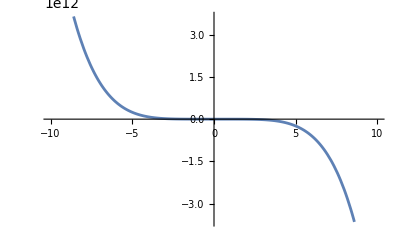

```mathematica
Clear["`*"];

terms={a0,a1,a2,a3,a4};

triRowsLHS[i_,j_,D_,n_]:=Module[{},
If[i-1==j,1,
If[i==j,D,
If[i+1==j,1,0]
]
]
]

triRowsRHS[i_,j_,a_,n_]:=Module[{},
If[i==1&&j<=5,terms[[j]],
If[i==n&&j>n-5,-terms[[n-j+1]],
If[i-1==j,-a,
If[i+1==j,a,0]
]
]
]
]

(*Generate 5x5 LHS and RHS Matrices*)
LHS=Array[triRowsLHS[#1,#2,D,5]&,{5,5}];
RHS=Array[triRowsRHS[#1,#2,a,5]&,{5,5}];
LHS//MatrixForm
RHS//MatrixForm


characteristicPolynomial=Det[RHS-λ/h LHS];(*//FullSimplify*)
(*Solve[characteristicPolynomial==0,λ]*)


ϵ=0.12;

(*rules={D->4,a->3/4,a0->0,a1->3/4,a2->-51/8,a3->37/4,a4->-29/8,h->0.1};*)

rules={D->4,a->3/4,a0->-25/12,a1->4,a2->-3,a3->4/3,a4->-1/4,h->0.1};

eig=Eigenvalues[Inverse[LHS].RHS] 1/h/.rules
ComplexListPlot[eig]
Plot[characteristicPolynomial/.rules,{λ,-10,10}]
```

## Periodic

(D | 1 | 0 | 0 | 1
1 | D | 1 | 0 | 0
0 | 1 | D | 1 | 0
0 | 0 | 1 | D | 1
1 | 0 | 0 | 1 | D)

(0 | a | 0 | 0 | -a
-a | 0 | a | 0 | 0
0 | -a | 0 | a | 0
0 | 0 | -a | 0 | a
a | 0 | 0 | -a | 0)

(-10 a^4 h^4 λ-5 a^4 D h^4 λ-20 a^2 h^2 λ^3+10 a^2 D h^2 λ^3-5 a^2 D^3 h^2 λ^3-2 λ^5-5 D λ^5+5 D^3 λ^5-D^5 λ^5)/h^5

{0,0.-3.70147 ⅈ,0.+3.70147 ⅈ,0.-3.08916 ⅈ,0.+3.08916 ⅈ}

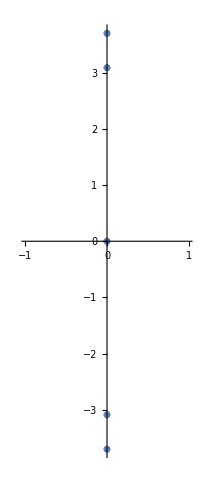

```mathematica
Clear["`*"];

terms={a0,a1,a2,a3,a4};

triRowsLHS[i_,j_,D_,n_]:=Module[{},
If[i==1&&j==5,1,
If[i==5&&j==1,1,
If[i-1==j,1,
If[i==j,D,
If[i+1==j,1,0]
]
]
]
]
]

triRowsRHS[i_,j_,a_,n_]:=Module[{},
If[i==1&&j==5,-a,
If[i==5&&j==1,a,
If[i-1==j,-a,
If[i+1==j,a,0]
]
]
]
]

(*Generate 5x5 LHS and RHS Matrices*)
LHS=Array[triRowsLHS[#1,#2,D,5]&,{5,5}];
RHS=Array[triRowsRHS[#1,#2,a,5]&,{5,5}];
LHS//MatrixForm
RHS//MatrixForm


characteristicPolynomial=Det[RHS-λ/h LHS](*//FullSimplify*)
(*Solve[%==0,λ]*)

ϵ=0.12;

rules={D->4,a->3/4,h->0.1};

(*rules={D->4,a->3/4,a0->-25/12,a1->4,a2->-3,a3->4/3,a4->-1/4,h->0.1};*)

eig=Eigenvalues[Inverse[LHS].RHS] 1/h/.rules
ComplexListPlot[eig]
```

## LHS Boundary Condition

(D | γ | 0 | 0 | 0
1 | D | 1 | 0 | 0
0 | 1 | D | 1 | 0
0 | 0 | 1 | D | 1
0 | 0 | 0 | γ | D)

(a0 | a1 | a2 | a3 | a4
-a | 0 | a | 0 | 0
0 | -a | 0 | a | 0
0 | 0 | -a | 0 | a
-a4 | -a3 | -a2 | -a1 | -a0)

{0,0.-6.8123 ⅈ,0.+6.8123 ⅈ,0.-5.86388 ⅈ,0.+5.86388 ⅈ}

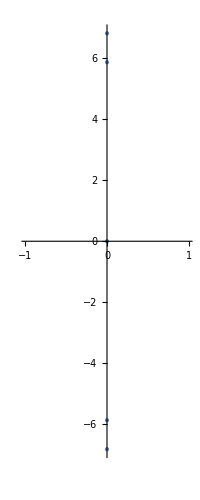

```mathematica
Clear["`*"];

terms={a0,a1,a2,a3,a4};

triRowsLHS[i_,j_,D_,n_]:=Module[{},
If[i==1&&j==2,γ,
If[i==n&&j==n-1,γ,
If[i-1==j,1,
If[i==j,D,
If[i+1==j,1,0]
]
]
]
]
]

triRowsRHS[i_,j_,a_,n_]:=Module[{},
If[i==1&&j<=5,terms[[j]],
If[i==n&&j>n-5,-terms[[n-j+1]],
If[i-1==j,-a,
If[i+1==j,a,0]
]
]
]
]

(*Generate 5x5 LHS and RHS Matrices*)
LHS=Array[triRowsLHS[#1,#2,D,5]&,{5,5}];
RHS=Array[triRowsRHS[#1,#2,a,5]&,{5,5}];
LHS//MatrixForm
RHS//MatrixForm


characteristicPolynomial=Det[RHS-λ/h LHS];(*//FullSimplify*)
(*Solve[%==0,λ]*)

ϵ=0.12;

rules={D->4,a->3/4,a0->0,a1->197/18,a2->-31/2,a3->11/2,a4->-17/18,γ->-25/3,h->0.1};

(*rules={D->4,a->3/4,a0->-25/12,a1->4,a2->-3,a3->4/3,a4->-1/4,h->0.1};*)

eig=Eigenvalues[Inverse[LHS].RHS] 1/h/.rules
ComplexListPlot[eig,PlotRange->All,PlotStyle->{PointSize->Medium},AspectRatio->Full]
```